```mathematica
D[-(x-x2)^2(-h+2(x1-x))/h^3,x]
```

-(2 (-h+2 (-x+x1)) (x-x2))/h^3+(2 (x-x2)^2)/h^3

```mathematica
D[(x-x1)(x-x2)^2/h^2,x]
```

(2 (x-x1) (x-x2))/h^2+(x-x2)^2/h^2

```mathematica
D[(x-x1)^2(h+2(x2-x))/h^3,x]
```

-(2 (x-x1)^2)/h^3+(2 (x-x1) (h+2 (-x+x2)))/h^3

```mathematica
m={{1,x1,x1^2,x1^3},{1,x2,x2^2,x2^3},{0,1,2x1,3x1^2},{0,1,2x2,3x2^2}}
```

{{1,x1,x1^2,x1^3},{1,x2,x2^2,x2^3},{0,1,2 x1,3 x1^2},{0,1,2 x2,3 x2^2}}

```mathematica
LinearSolve[m,{w1,w2,wx1,wx2}]
```

{1/(x1-x2)^3(w2 x1^3-3 w2 x1^2 x2-wx2 x1^3 x2+3 w1 x1 x2^2-wx1 x1^2 x2^2+wx2 x1^2 x2^2-w1 x2^3+wx1 x1 x2^3),1/(x1-x2)^3(wx2 x1^3-6 w1 x1 x2+6 w2 x1 x2+2 wx1 x1^2 x2+wx2 x1^2 x2-wx1 x1 x2^2-2 wx2 x1 x2^2-wx1 x2^3),1/(x1-x2)^3(3 w1 x1-3 w2 x1-wx1 x1^2-2 wx2 x1^2+3 w1 x2-3 w2 x2-wx1 x1 x2+wx2 x1 x2+2 wx1 x2^2+wx2 x2^2),(-2 w1+2 w2+wx1 x1+wx2 x1-wx1 x2-wx2 x2)/(x1-x2)^3}

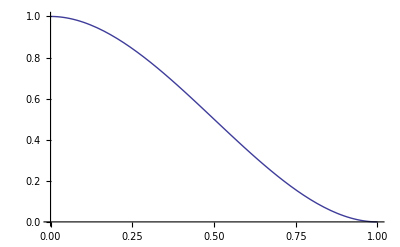

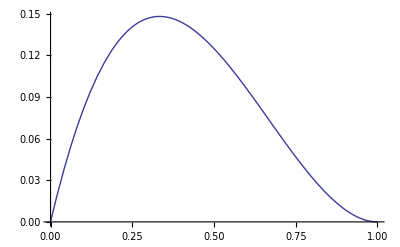

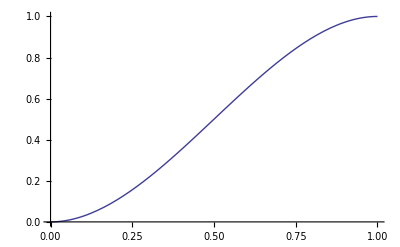

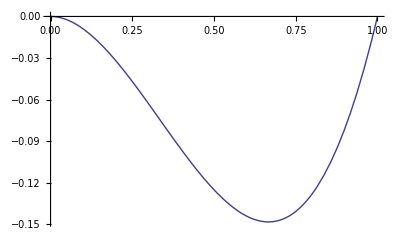

```mathematica
Plot[-(x-1)^2(-1+2(0-x))/1^3,{x,0,1}]
Plot[(x-0)(x-1)^2/1^3,{x,0,1}]
Plot[(x-0)^2(1+2(1-x))/1^3,{x,0,1}]
Plot[(x-0)^2(x-1)/1^3,{x,0,1}]
```

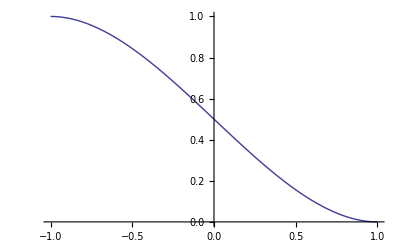

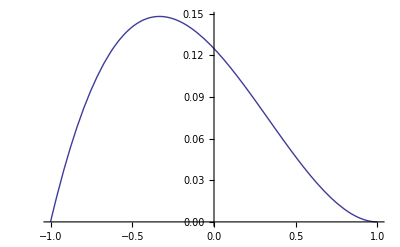

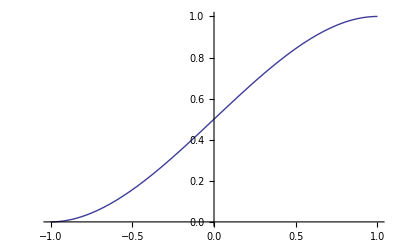

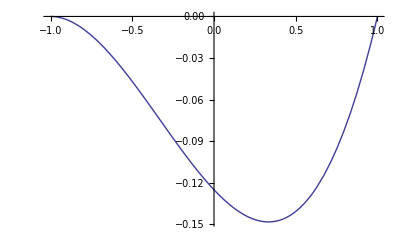

```mathematica
Plot[1/4(x-1)^2(x+2),{x,-1,1}]
Plot[1/8(x+1)(x-1)^2,{x,-1,1}]
Plot[-1/4(x-2)(x+1)^2,{x,-1,1}]
Plot[1/8(x+1)^2(x-1),{x,-1,1}]
```

```mathematica
Simplify[D[1/4(x-1)^2(x+2),{x,2}]]
Simplify[D[h/8(x+1)(x-1)^2,{x,2}]]
Simplify[D[-1/4(x-2)(x+1)^2,{x,2}]]
Simplify[D[h/8(x+1)^2(x-1),{x,2}]]
```

(3 x)/2

1/4 h (-1+3 x)

-(3 x)/2

1/4 h (1+3 x)

```mathematica
Simplify[1/2(-1-x)^2-1/2(1-x)^2]
Simplify[1/6(-1-x)^3-1/6(1-x)^3]
Simplify[1/12(-1-x)^4-1/12(1-x)^4]
Simplify[1/2(-1-x)^2+1/2(1-x)^2]
Simplify[1/6(-1-x)^3+1/6(1-x)^3]
Simplify[1/12(-1-x)^4+1/12(1-x)^4]
```

2 x

-1/3-x^2

2/3 (x+x^3)

1+x^2

-1/3 x (3+x^2)

1/6 (1+6 x^2+x^4)

```mathematica
Simplify[1/2*x^2(1+x^2)-x^2/2(3+x^2)+1/2(1/3+x^2)]
```

1/6 (1-3 x^2)

```mathematica
Simplify[1/5!((-1-x)^5-(1-x)^5)]
```

1/60 (-1-10 x^2-5 x^4)

```mathematica
Simplify[1/4!((-1-x)^4+(1-x)^4)]
```

1/12 (1+6 x^2+x^4)

```mathematica
Simplify[1/4!((-1-x)^4-(1-x)^4)]
```

1/3 (x+x^3)

```mathematica
Simplify[3x/2(1/60 (-1-10 x^2-5 x^4)+1/12 (1+6 x^2+x^4))+1/2 1/3 (x+x^3)]
```

2/15 x (2+5 x^2)

```mathematica
Plot[(x-1)^2(2x+1),{x,0,1}];
Plot[x(x-1)^2,{x,0,1}];
Plot[x^2(3-2x),{x,0,1}];
Plot[x^2(x-1),{x,0,1}];
Simplify[D[(x-1)^2(2x+1),{x}]]
Simplify[D[(x-1)^2(2x+1),{x,2}]]
Simplify[D[x(x-1)^2,{x}]]
Simplify[D[x(x-1)^2,{x,2}]]
```

6 (-1+x) x

-6+12 x

1-4 x+3 x^2

-4+6 x

```mathematica
Integrate[(-6+12 x)^2,{x,0,1}]
Integrate[(-6+12 x)(-4+6 x),{x,0,1}]
Integrate[(-4+6 x)^2,{x,0,1}]
Integrate[(x-1)^2(2x+1),{x,0,1}]
Integrate[x(x-1)^2,{x,0,1}]
```

12

6

4

1/2

1/12

```mathematica
LinearSolve[{{12,6},{6,4}},{c/2+Q,c/12-M}]
```

{1/24 (3 c+12 M+8 Q),1/6 (-c-6 M-3 Q)}

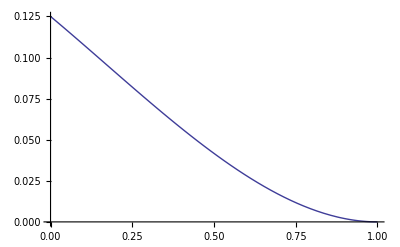

```mathematica
Plot[1/8(x-1)^2(2x+1)-1/6x(x-1)^2,{x,0,1}]
```

```mathematica
Simplify[D[1/4(x-1)^2(x+2),{x,2}]]
Simplify[D[h/8(x+1)(x-1)^2,{x,2}]]
Simplify[D[-1/4(x-2)(x+1)^2,{x,2}]]
Simplify[D[h/8(x+1)^2(x-1),{x,2}]]
```

(3 x)/2

1/4 h (-1+3 x)

-(3 x)/2

1/4 h (1+3 x)

```mathematica
8EI/h^3Integrate[((3 x)/2)((3 x)/2),{x,0,1}]
8EI/h^3Integrate[(1/4 h (-1+3 x))((3 x)/2),{x,0,1}]
8EI/h^3Integrate[(-(3 x)/2)((3 x)/2),{x,0,1}]
8EI/h^3Integrate[(1/4 h (1+3 x))((3 x)/2),{x,0,1}]
```

(6 EI)/h^3

(3 EI)/(2 h^2)

-(6 EI)/h^3

(9 EI)/(2 h^2)

```mathematica
8EI/h^3Integrate[(1/4 h (-1+3 x))(1/4 h (-1+3 x)),{x,0,1}]
8EI/h^3Integrate[(-(3 x)/2)(1/4 h (-1+3 x)),{x,0,1}]
8EI/h^3Integrate[(1/4 h (1+3 x))(1/4 h (-1+3 x)),{x,0,1}]
```

(3 EI)/(2 h^2)

EI/(2 h)

-(3 EI)/(2 h^2)

EI/h

```mathematica
8EI/h^3Integrate[(-(3 x)/2)(-(3 x)/2),{x,0,1}]
8EI/h^3Integrate[(1/4 h (1+3 x))(-(3 x)/2),{x,0,1}]
```

(6 EI)/h^3

-(9 EI)/(2 h^2)

```mathematica
8EI/h^3Integrate[(1/4 h (1+3 x))(1/4 h (1+3 x)),{x,0,1}]
```

(7 EI)/(2 h)